```mathematica
(* 1838 and 2013 tables *)
```

```mathematica
dat={{100000,83641,78263,75435,73685,72372,71388,70616,69969,69435,68986,68598,68251,67926,67606,67278,66930,66553,66140,65697,65190,64650,64103,63549,62928,62422,61850,61273,60691,60103,59509,58909,58304,57691,57072,56444,55808,55163,54508,53842,53166,52475,51773,51057,50325,49577,48813,48031,47231,46411,45573,44714,43810,42830,41926,40946,39941,38909,37848,36737,35633,34474,33279,32045,30772,29456,28106,26716,25290,23833,22349,20845,19330,17811,16300,14808,13345,11925,10559,9257,8034,6895,5847,4827,4047,3298,2648,2093,1627,1243,932,686,495,349,241,160,107,69,43,25,15}/10^5,
{100000,99571,99539,99522,99510,99500,99492,99483,99473,99466,99457,99448,99438,99428,99417,99405,99388,99368,99338,99297,99250,99204,99155,99108,99055,99001,98944,98883,98820,98757,98690,98618,98543,98457,98372,98278,98177,98070,97954,97820,97683,97532,97370,97197,97016,96816,96599,96369,96122,95864,95576,95268,94938,94587,94205,93782,93326,92827,92272,91664,90997,90262,89474,88616,87687,86681,85612,84495,83278,81962,80502,78933,77231,75319,73287,71065,68715,66214,63563,60716,57713,54455,51050,47415,43644,39781,35788,31812,27881,24024,20360,16934,13821,10983,8482,6432,4732,3414,2370,1578,1024}/10^5};
```

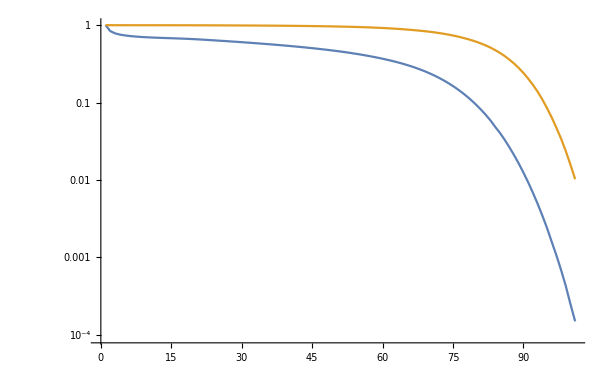

```mathematica
ListLogPlot[dat,Joined->True,GridLines->Automatic]
```

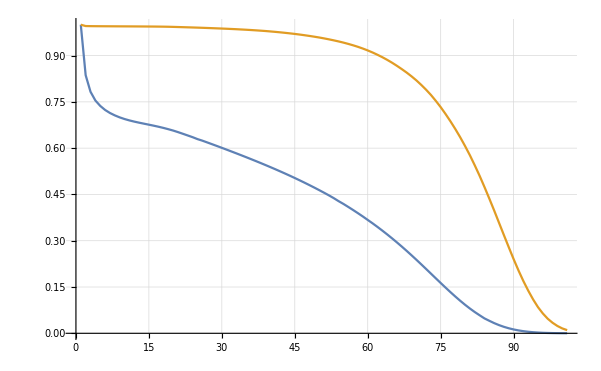

```mathematica
ListPlot[dat,Joined->True,GridLines->Automatic]
```

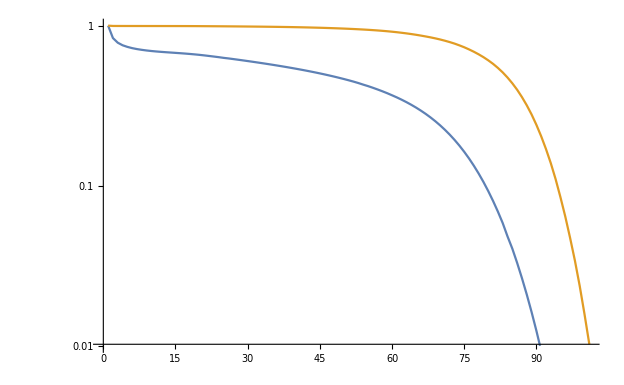

```mathematica
ListLogPlot[dat,Joined->True,GridLines->Automatic,PlotRange->{.01,1}]
```

```mathematica
datm={{0.18305,0.06643,0.0368,0.02347,0.01798,0.01369,0.01087,0.0092,0.00766,0.00649,0.00564,0.00507,0.00477,0.00472,0.00486,0.00519,0.00565,0.00622,0.00672,0.00775,0.00832,0.0085,0.00868,0.00982,0.00807,0.00921,0.00937,0.00954,0.00974,0.00993,0.01013,0.01032,0.01057,0.01079,0.01106,0.01133,0.01162,0.01194,0.01229,0.01263,0.01308,0.01347,0.01393,0.01444,0.01497,0.01553,0.01615,0.0168,0.01751,0.01822,0.01903,0.02042,0.02262,0.02133,0.02365,0.02485,0.02618,0.02765,0.02979,0.03051,0.03306,0.03528,0.03778,0.04053,0.0437,0.04691,0.05071,0.05484,0.05932,0.06427,0.06964,0.07542,0.0818,0.08859,0.09592,0.10393,0.11239,0.12151,0.13141,0.14146,0.15259,0.1645,0.19112,0.17579,0.20395,0.21863,0.23413,0.25054,0.2676,0.28598,0.30408,0.32345,0.34597,0.3661,0.40399,0.397,0.43182,0.46429,0.52941,0.5,0.8059},{0.00431,0.00032,0.00017,0.00012,0.0001,0.00009,0.00009,0.0001,0.00007,0.00009,0.0001,0.00009,0.0001,0.00012,0.00012,0.00016,0.00021,0.00029,0.00042,0.00048,0.00046,0.00049,0.00047,0.00054,0.00054,0.00059,0.00062,0.00064,0.00063,0.00068,0.00073,0.00076,0.00087,0.00087,0.00095,0.00103,0.00109,0.00119,0.00136,0.0014,0.00155,0.00166,0.00178,0.00186,0.00207,0.00225,0.00238,0.00256,0.00269,0.00301,0.00323,0.00347,0.00371,0.00404,0.0045,0.00488,0.00536,0.006,0.0066,0.00731,0.00811,0.00876,0.00964,0.01054,0.01154,0.01241,0.01314,0.01451,0.01593,0.01797,0.01969,0.0218,0.02506,0.02736,0.03078,0.03362,0.03708,0.04085,0.04582,0.05071,0.0581,0.06454,0.07385,0.08281,0.0926,0.10568,0.11763,0.13171,0.14865,0.1651,0.18369,0.20244,0.22888,0.25694,0.27489,0.3045,0.32371,0.36101,0.40111,0.42626,0.6018}};
datmf={{0.1468,0.06537,0.03548,0.02421,0.01797,0.01343,0.01054,0.00912,0.0066,0.00773,0.00596,0.0053,0.00512,0.00507,0.00626,0.00456,0.00645,0.00614,0.00721,0.0079,0.0086,0.00882,0.00935,0.00895,0.00961,0.0095,0.01033,0.00957,0.01186,0.00882,0.01063,0.01082,0.01102,0.01123,0.01435,0.00875,0.01185,0.0121,0.01231,0.01316,0.0123,0.01314,0.0134,0.01371,0.01402,0.01439,0.01472,0.0151,0.01536,0.01603,0.01635,0.0168,0.01729,0.0178,0.01987,0.0212,0.02259,0.02407,0.02566,0.02739,0.02901,0.03161,0.03363,0.03614,0.03892,0.04199,0.04535,0.04908,0.05315,0.05761,0.06248,0.06778,0.07355,0.0798,0.08659,0.09388,0.10172,0.1102,0.11922,0.12892,0.13926,0.15026,0.16199,0.17445,0.18761,0.2016,0.21629,0.23227,0.24776,0.26548,0.2834,0.30245,0.32205,0.34337,0.36419,0.38711,0.41109,0.43478,0.46301,0.48329,0.7316},{0.00349,0.00026,0.00013,0.00011,0.00008,0.00007,0.00007,0.00008,0.00007,0.00007,0.00007,0.00006,0.00006,0.00011,0.00011,0.00014,0.00016,0.00015,0.0002,0.00021,0.0002,0.0002,0.00021,0.00023,0.00021,0.00025,0.00028,0.00026,0.00033,0.00034,0.00038,0.00041,0.00045,0.00047,0.00053,0.00059,0.00065,0.00067,0.00074,0.00083,0.00091,0.00095,0.00108,0.00116,0.00128,0.00139,0.00148,0.00161,0.00175,0.0019,0.00216,0.00231,0.00253,0.0028,0.003,0.00337,0.00363,0.00401,0.00425,0.00471,0.00525,0.00574,0.00623,0.00682,0.00734,0.00802,0.00852,0.00953,0.01073,0.01171,0.0131,0.01444,0.01625,0.01845,0.02052,0.02269,0.02539,0.02823,0.0314,0.03606,0.04139,0.04671,0.05334,0.0605,0.06989,0.07901,0.08928,0.10225,0.11468,0.13091,0.14875,0.16488,0.18628,0.21136,0.23385,0.25522,0.27836,0.31009,0.34203,0.37752,0.51297}};
```

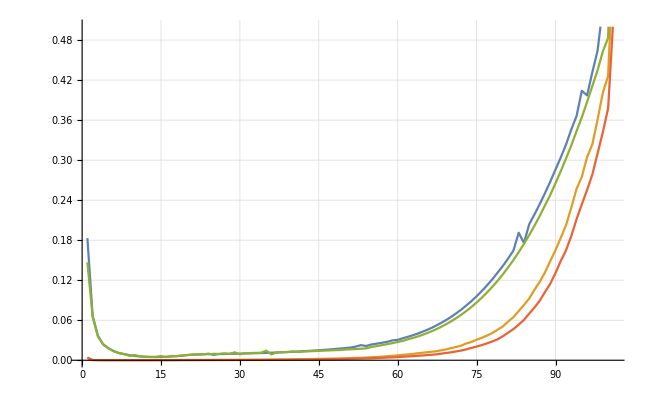

```mathematica
ListPlot[datm~Join~datmf,Joined->True,GridLines->Automatic,PlotRange->{All,{0,.5}}]
```

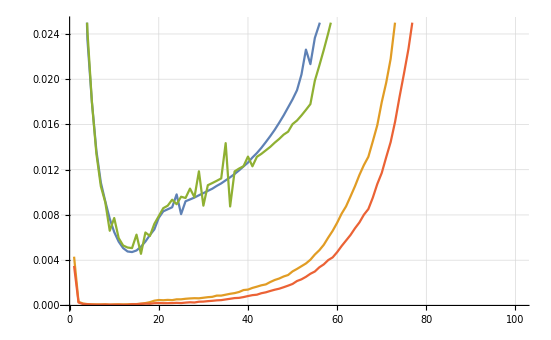

```mathematica
ListPlot[datm~Join~datmf,Joined->True,GridLines->Automatic,PlotRange->{All,{0,.025}}]
```

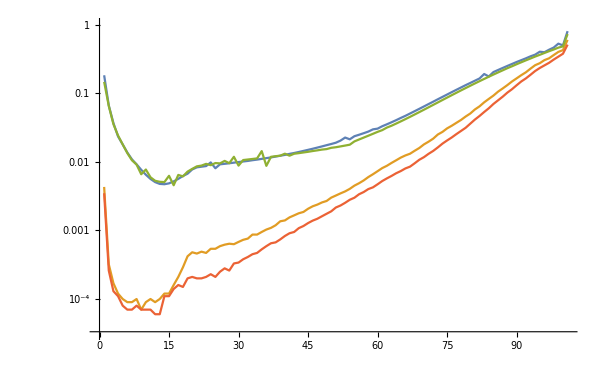

```mathematica
ListLogPlot[datm~Join~datmf,Joined->True,GridLines->Automatic,PlotRange->{All,{10^-4.5,1}}]
```

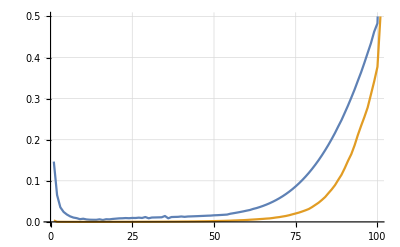

```mathematica
ListPlot[datmf,Joined->True,GridLines->Automatic,PlotRange->{{0,100},{0,.5}}]
```

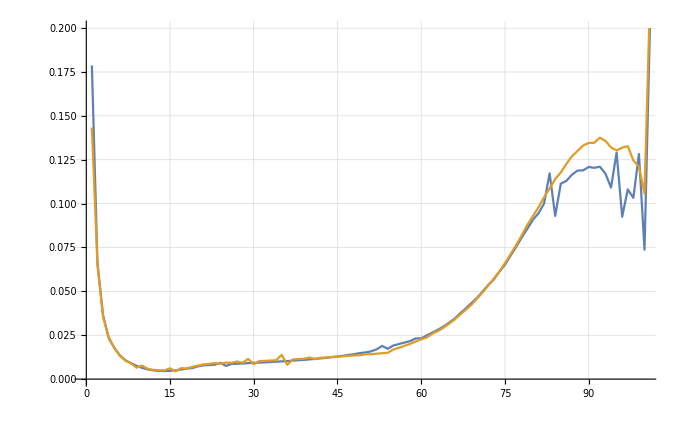

```mathematica
ListPlot[{datm[[1]]-datm[[2]],datmf[[1]]-datmf[[2]]},Joined->True,GridLines->Automatic,PlotRange->{{0,100},{0,.2}}]
```

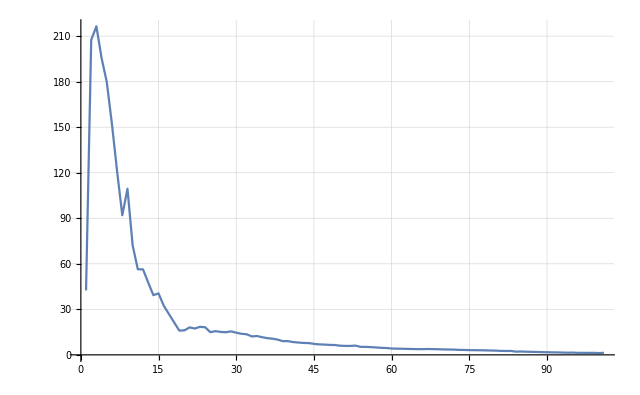

```mathematica
ListPlot[datm[[1]]/datm[[2]],Joined->True,GridLines->Automatic,PlotRange->All]
```